# Utilisation avancée de Mathematica

## UPEC, Paris.

Guillaume Saës (guillaume.saes@u-pec.fr)

## Palettes et raccourcis clavier

Les diverses palettes (voir menu "Palettes", puis par exemple "Classroom Assistant") permettent de trouver facilement les commandes Mathematica les plus courantes et de taper des formules mathématiques avec le format d'écriture naturel. Par exemple, elles permettent de taper l'expression suivante

```mathematica
(x^2+3)Exp[-y]/(z+Pi)
```

(ⅇ^-y (3+x^2))/(π+z)

sous une forme plus lisible

```mathematica
((x^2+3)ⅇ^-y)/(z+π)
```

(ⅇ^-y (3+x^2))/(π+z)

Pour taper plus vite, il est également utile de connaitre quelques raccourcis clavier :

- Ctrl+6 : pour faire les puissances (exemple : x^2)

- Ctrl+/ : pour faire les fractions (exemple : 1/2)

- EsceeEsc : pour écrire l'exponentielle ⅇ (équivalent à Exp)

- EscpEsc : pour écrire le nombre π (équivalent à Pi)

- EsciiEsc : pour écrire le nombre imaginaire ⅈ (équivalent à I)

- EscinfEsc : pour écrire ∞ (équivalent à Infinity)

- Esc->Esc : pour écrire → (équivalent à ->)

etc...

## Listes

Dans Mathematica, on utilise souvent les listes qui sont des ensembles d'éléments regroupés entre accolades et séparés par des virgules. Par exemple,

```mathematica
{a,b,c}
```

{a,b,c}

est une liste. Les éléments a, b,... d'une liste peuvent être n'importe quoi (nombre, variables, fonctions, ...) y compris une liste eux-mêmes !  On peut donc imaginer des listes imbriquées complètement générales du genre :

```mathematica
{{a,3},b,{coucou,h[x],-56}}
```

{{a,3},b,{coucou,h[x],-56}}

Nous verrons plus loin qu'une liste simple du type {a,b,c} représente un vecteur de dimension 3 et qu'une liste de listes du type {{a,b},{c,d},{e,f}} représente une matrice de dimension 3×2.

On peut bien sûr affecter une liste à une variable :

```mathematica
maliste={{a,b},{1,2},-5}
```

{{a,b},{1,2},-5}

On peut accéder individuellement au ième élément d'une liste avec la syntaxe suivante [[i]], par exemple :

```mathematica
maliste[[2]]
```

{1,2}

```mathematica
maliste[[3]]
```

-5

Un détail : on peut utiliser les raccourcis clavier Esc[[Esc et Esc]]Esc  pour rendre les doubles crochets plus jolis et plus lisibles :

```mathematica
maliste⟦2⟧
```

{1,2}

Il existe dans Mathematica beaucoup de fonctions de manipulation des listes (pour ajouter des éléments, en extraire, etc...). Consultez l'aide si besoin.

On peut visualiser l’architecture d’une liste sous forme d’arbre :

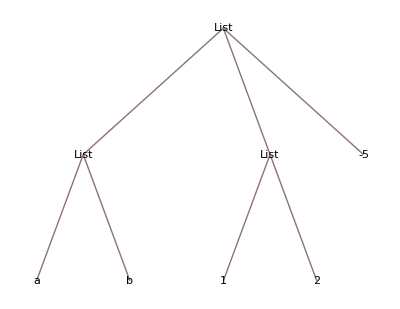

```mathematica
TreeForm[maliste]
```

## Substitution

L'opération "/." (correspondant à une fonction appelée "ReplaceAll" en Mathematica) permet de substituer dans une expression une variable par une valeur ou par une autre variable. Par exemple, pour remplacer z par 2 dans l'expression (z+1)^2, on peut écrire

```mathematica
(z+1)^2/.z->2
```

9

"z -> 2" s'appelle une règle ("rule" en anglais) de substitution. L'avantage est que "2" n'est pas affecté à la variable z globalement dans tout le notebook, mais la substitution ne se fait que localement dans l'expression ci-dessus, et on peut continuer à utiliser z par la suite comme une variable non définie :

```mathematica
z
```

z

On peut faire plusieurs substitutions avec la syntaxe suivante

```mathematica
{z+1,abc^2}/.{z->2,abc->m}
```

{3,m^2}

Souvent les fonctions Mathematica retournent les résultats sous forme d'une liste de règles, par exemple

```mathematica
resultat=Solve[x^2-x-2==0,x]
```

{{x→-1},{x→2}}

où nous avons stocké le résultat dans la variable "resultat". La première solution x=-1 correspond au premier élément de la liste "resultat" :

```mathematica
resultat⟦1⟧
```

{x→-1}

Puisque "resultat⟦1⟧" est sous la forme d'une règle, il suffit d'appliquer une substitution sur la variable "x" pour extraire la valeur "-1" :

```mathematica
x/.resultat⟦1⟧
```

-1

## Pipeline

L'opération "//" (appelée "pipeline", ou tube en français) permet d'appliquer une fonction au dernier résultat avec un syntaxe inversée. Ainsi, l'instruction suivante

```mathematica
x//f
```

f[x]

est équivalente à

```mathematica
f[x]
```

f[x]

L'exemple ci-dessus ne présente pas vraiment d'intérêt et rend l'écriture beaucoup moins claire. En revanche, le pipeline est très pratique pour appliquer une fonction Mathematica à une expression déjà tapée sans avoir à revenir au début de la ligne, par exemple :

```mathematica
(Cos[x]+Sin[x])^2-2Cos[x] Sin[x]//Expand
```

Cos[x]^2+Sin[x]^2

On peut empiler plusieurs fonctions avec les pipelines, par exemple appliquons la fonction "Simplify" au résultat précédent

```mathematica
(Cos[x]+Sin[x])^2-2Cos[x] Sin[x]//Expand//Simplify
```

1

Autre exemple, appliquons la fonction "N" au nombre π avec un pipeline

```mathematica
π//N
```

3.14159

Il est également possible d'utiliser le pipeline pour appliquer une fonction avec plus d'un seul argument, on utilise alors la syntaxe suivante

```mathematica
π//N[#,100]&
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

qui est équivalent à

```mathematica
N[π,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

Le symbole "#" repère l'endroit où l'expression qui précède (ici π) sera insérée et "&" marque la fin de la fonction. La simplicité de la syntaxe est néanmoins un peu perdue.

## Structure conditionnelle If

La structure conditionnelle “If” permet de choisir d’exécuter une instruction ou une autre suivant qu’une condition (appelée expression logique en informatique) est vraie ou fausse. La syntaxe est la suivante : “If [expression logique, instruction1, instruction2]”. Si “expression logique” est vraie (“True” en Mathematica) alors uniquement “instruction1” sera exécutée; si au contraire “expression logique” est fausse (“False” en Mathematica) alors uniquement “instruction2” sera exécutée.

Par exemple, utilisons une structure “If” pour écrire la fonction f(x) définie par morceaux : 
f(x)=-x si x≤0 et f(x)=x.b2 si x>0

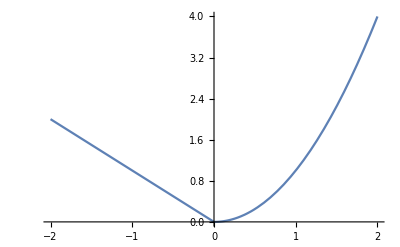

```mathematica
f[x_]:=If[x≤0,-x,x^2]
Plot[f[x],{x,-2,2}]
```

voici quelques exemples d’expressions logiques pouvant être utilisées dans un “If” :

```mathematica
-2==3
```

False

```mathematica
-2≠3
```

True

On peut aussi combiner des expressions logiques avec un ET logique (“&&” en Mathematica) ou “OU” logique (“| |” en Mathematica). Par exemple, pour tester si -2< 0 ET 3 = 0, on écrit

```mathematica
-2<0 && 3==0
```

False

pour tester si -2<0 OU 3=0, on écrit :

```mathematica
-2<0 || 3==0
```

True

La fonction Boole permet de renvoyer 0 ou 1 à la place respective de “False” et “True” :

```mathematica
Boole[-2<0]
```

1

```mathematica
Boole[-2>0]
```

0

## Les boucles Do... / While... et For...

### Do...

Une boucle "Do" permet d'exécuter plusieurs fois une instruction.  La commande "Do[instruction, {i, debut, fin}]" fait varier l'entier "i" (appelé "itérateur") de l'entier "debut" à l'entier "fin" et exécute à chaque fois "instruction". Par exemple, pour afficher "Coucou" 5 fois, on utilise une boucle Do exécutant l'instruction Print["Coucou"] lorsque i varie de 1 jusqu'à 5 :

```mathematica
Do[Print["Coucou"],{i,1,5}]
```

Coucou

Coucou

Coucou

«2 more identical outputs»

ce qui ne semble pas servir à grand chose... Les boucles Do sont plus intéressantes si on a besoin d'utiliser l'entier i dans l'instruction. Par exemple, affichons les 10 premiers entiers

```mathematica
Do[Print[i],{i,1,10}]
```

1

2

3

4

5

6

7

8

9

10

Plus intéressant encore, utilisons une boucle Do pour calculer la somme des 100 premiers entiers s=∑_(i=1)^100 i. On commence par initialiser la variable s à 0

```mathematica
s=0
```

0

puis on fait varier i de 1 jusqu'à 100 et à chaque itération on calcule s+i et on affecte le résultat à la variable s

```mathematica
Do[s=s+i,{i,1,100}]
```

A la fin des itérations, la variable  s contient la somme recherchée

```mathematica
s
```

5050

Il est souvent plus clair (et plus sûr) de regrouper ces trois instructions en une seule instruction dans une seule cellule en les séparant par des ";" (qui permettent de supprimer les affichages intermédiaires)

```mathematica
s=0;
Do[s=s+i,{i,1,100}];
s
```

5050

Il se trouve que Mathematica dispose d'une fonction "Sum" permettant de faire cette somme plus directement

```mathematica
Sum[i,{i,1,100}]
```

5050

Néanmoins, les boucles Do permettent de faire beaucoup plus de choses.

Par défaut, l'itérateur varie par incrément de 1, mais on peut aussi utiliser n'importe quel autre incrément. Par exemple, dans la boucle Do suivante l'entier j varie de 3 jusqu'à 10 par incrément de 2

```mathematica
Do[Print[j],{j,3,10,2}]
```

3

5

7

9

Et dans la boucle suivante l'entier j varie de 5 jusqu'à 2 par incrément de -1

```mathematica
Do[Print[j],{j,5,2,-1}]
```

5

4

3

2

Enfin, on peut exécuter plusieurs instructions dans une boucle Do en les séparant par ";". Par exemple, calculons la somme s et le produit p des 10 premiers entiers, s=∑_(i=1)^10 i et p=∏_(i=1)^10 i, avec une seule boucle Do :

```mathematica
s=0;
p=1;
Do[
s=s+i;
p=p*i,{i,1,10}];
Print[s];
Print[p];
```

55

3628800

Les retours à la ligne ne sont pas obligatoires mais facilitent la lecture.

### While...

Une boucle “While” permet d’exécuter une instruction tant qu’une condition est remplie “While[condition,instruction]”.

```mathematica
S=10;
While[S≥5,{Print[S],S=S-1}]
```

10

9

8

7

6

5

### For...

Une boucle “For” permet d’exécuter plusieurs fois une instruction tant qu’une condition est remplie “For[Début,Test,Incrément,instruction]”.

```mathematica
For[i=0,i≤5,i++,Print[i]]
```

0

1

2

3

4

5

```mathematica
S=0;
For[i=0,i≤10 && S<5,i++,{S=S+i,Print[S]}]
```

0

1

3

6

## Calcul vectoriel

En Mathematica, les composantes d'un vecteur s'écrivent avec une liste simple, c'est-à-dire qu'elles sont regroupées entre accolades et séparées par des virgules. Par exemple, dans un espace de dimension 3, définissons le vecteur u suivant :

```mathematica
u={2,-3}
```

{2,-3}

Chaque composante d'un vecteur est individuellement accessible (et modifiable) avec la syntaxe u[[i]] où i est le numéro de la composante. Ainsi, la 2ème composante s'obtient par

```mathematica
u[[2]]
```

-3

ou en utilisant les raccourcis clavier Esc[[Esc et Esc]]Esc  pour rendre les doubles crochets plus jolis et plus lisibles :

```mathematica
u⟦2⟧
```

-3

On peut faire un certain nombre d'opérations sur ce vecteur. Par exemple, une multiplication par un scalaire :

```mathematica
3 u
```

{6,-9}

ou le calcul de sa norme  :

```mathematica
Norm[u]
```

√13

Définissons maintenant un deuxième vecteur v

```mathematica
v={4,-1}
```

{4,-1}

En Mathematica, la multiplication directe u * v (ou simplement u  v) signifie multiplier la ième composante de u avec la même ième composante de v

```mathematica
u* v
```

{8,3}

Le produit scalaire est obtenu par l'opération "."

```mathematica
u.v
```

11

## Calcul matriciel

En Mathematica, une matrice est définie comme une liste de vecteurs lignes. Par exemple, définissons la matrice A suivante de dimension 3×3

```mathematica
A={{1,1,0},{2,-2,0},{0,0,3}}
```

{{1,1,0},{2,-2,0},{0,0,3}}

On peut utiliser la fonction "MatrixForm" (par exemple en pipeline) pour afficher la matrice sous forme plus claire

```mathematica
A//MatrixForm
```

(1 | 1 | 0
2 | -2 | 0
0 | 0 | 3)

La syntaxe A⟦i,j⟧ (ou A⟦i⟧⟦j⟧ ) permet d'accéder à l'élement (i,j) de A, par exemple

```mathematica
A⟦2,1⟧
```

2

Essayons quelques opérations sur cette matrice :

- multiplication par un scalaire

```mathematica
3A
```

{{3,3,0},{6,-6,0},{0,0,9}}

- calcul de la transposée

```mathematica
Transpose[A]//MatrixForm
```

(1 | 2 | 0
1 | -2 | 0
0 | 0 | 3)

- calcul de la trace

```mathematica
Tr[A]
```

2

- calcul du déterminant

```mathematica
Det[A]
```

-12

- calcul de la matrice inverse

```mathematica
Inverse[A]
```

{{1/2,1/4,0},{1/2,-1/4,0},{0,0,1/3}}

- calcul du cube de la matrice, A^3

```mathematica
MatrixPower[A,3]
```

{{1,5,0},{10,-14,0},{0,0,27}}

- calcul des valeurs propres et des vecteurs propres

```mathematica
Eigenvalues[A]
```

{3,1/2 (-1-√17),1/2 (-1+√17)}

```mathematica
Eigenvectors[A]
```

{{0,0,1},{1+1/4 (-1-√17),1,0},{1+1/4 (-1+√17),1,0}}

Définissons maintenant une deuxième matrice rectangulaire B

```mathematica
B={{-3,2},{1,0},{7,8}}
```

{{-3,2},{1,0},{7,8}}

```mathematica
B//MatrixForm
```

(-3 | 2
1 | 0
7 | 8)

Le produit matriciel de A par B se calcule avec l'opération "."

```mathematica
A.B
```

{{-2,2},{-8,4},{21,24}}

Par contre, les dimensions de ces matrices interdissent le produit matriciel de B par A  et Mathematica ne s'y trompe pas et refuse de le faire

```mathematica
B.A
```

Dot::dotsh: Tensors {{-3, 2}, {1, 0}, {7, 8}} and {{1, 1, 0}, {2, -2, 0}, {0, 0, 3}} have incompatible shapes.

{{-3,2},{1,0},{7,8}}.{{1,1,0},{2,-2,0},{0,0,3}}